```mathematica
r[u_,v_]={2 u v,u^2 - v^2}
```

{2 u v,u^2-v^2}

```mathematica
U0={3/4,-1}
```

{3/4,-1}

```mathematica
dU = {1/4,3/8}
```

{1/4,3/8}

```mathematica
u0 = U0[[1]]; du = dU[[1]]; v0 = U0[[2]]; dv = dU[[2]];
```

```mathematica
R0 = r[u0,v0]
```

{-3/2,-7/16}

```mathematica
e1 = D[r[u,v],u]/Norm[D[r[u,v],u]]/. {u->u0,v->v0}
```

{-4/5,3/5}

```mathematica
e2 = D[r[u,v],v]/Norm[D[r[u,v],v]]/. {u->u0,v->v0}
```

{3/5,4/5}

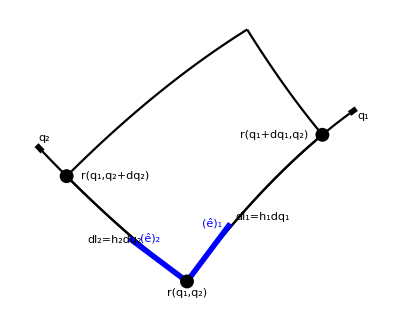

```mathematica
area = Show[
ParametricPlot[Table[r[u,v],{u,u0,u0+du,du}],{v, v0,v0+dv},
Epilog->{PointSize[0.025],Point[R0]},PlotStyle->Black],ParametricPlot[Table[r[u,v],{v,v0,v0+dv,dv}],{u, u0,u0+du},PlotStyle->Black],ParametricPlot[r[u,v0],{u,u0,u0+1.23 du},PlotStyle->Black],ParametricPlot[r[u0,v],{v,v0,v0+1.20 dv},PlotStyle->Black],
Graphics[{Thickness[0.01],
Blue,
Arrow[{R0,R0+0.3e1}],
Arrow[{R0,R0+0.3e2}],
Black,
Text[Style["q_2",Medium],r[u0+1.25 du, v0 ]+{0.03,0.03}],
Text[Style["q_1",Medium],r[u0,v0+1.25 dv ]+{0.03,-0.03}],
Text[Style["r(q_1,q_2)",Medium],R0+{0,-0.05}],
Text[Style["r(q_1,q_2+dq_2)",Medium],
r[u0+du,v0]+{0.2,0}],
Text[Style["r(q_1+dq_1,q_2)",Medium],
r[u0,v0+dv]-{0.2,0}],
{Blue,Text[Style["(ê)_2",Medium],
R0+0.3e1-{-0.085,0}],
Text[Style["(ê)_1",Medium],
R0+0.3e2-{0.075
,0}]},
PointSize[0.025],Point[r[u0,v0+dv]],
PointSize[0.025],Point[r[u0+du,v0]],
Arrow[{r[u0+1.2 du, v0 ],
r[u0+1.25 du, v0 ]}],
Arrow[{r[u0, v0 +1.2 dv ],r[u0, v0 +1.25 dv ]
}],
Text[Style["dl_1=h_1dq_1",Medium],1/2(r[u0,v0]+r[u0,v0+dv])+{0.035,-0.035},{0,0},{1,1}],
Text[Style["dl_2=h_2dq_2",Medium],1/2(r[u0,v0]+r[u0+du,v0])+{-0.05,-0.045},{0,0},{1,-1}]
}],
Frame->None,Axes->None,
PlotRange->All
]
```